```mathematica
ClearAll["Global`*"];
```

```mathematica
$Assumptions=Element[{m,s},Integers]&&Element[{a,M,Q,r,z,ω},Reals]&&-1<z<1;
```

## ZSlice solver

## Reduced Held Operators

```mathematica
(*Reduced Held Operators*)
(*Pole-factorized Held operators in outgoing Kerr coordinates*)

(*----------assumptions----------*)
$Assumptions=Element[{m,s},Integers]&&Element[{a,M,r,z,ω},Reals]&&-1<z<1;

(*----------Kerr background in outgoing coordinates----------*)
Δ[r_]:=r^2-2 M r+a^2;
Σ[r_,z_]:=r^2+a^2 z^2;

Sfac[z_]:=Sqrt[1-z^2];

(*----------pole factor----------*)
alpha[m_,s_]:=Abs[m+s]/2;
beta[m_,s_]:=Abs[m-s]/2;

W[m_,s_][z_]:=(1-z)^alpha[m,s] (1+z)^beta[m,s];

(*----------spin from GHP weights,if you want to use p,q----------*)
spinFromPQ[p_,q_]:=(p-q)/2;

(*----------raw Held operators acting on an expression expr[r,z]----------*)
(*These match  current C++ edth_core_RSlice_with_extrapolation conventions.*)

EthHRaw[m_,s_,ω_][expr_]:=1/Sqrt[2]*(Sfac[z] D[expr,z]+((m+s z)/Sfac[z]-a ω Sfac[z]) expr);

EthBarHRaw[m_,s_,ω_][expr_]:=1/Sqrt[2]*(Sfac[z] D[expr,z]-((m+s z)/Sfac[z]-a ω Sfac[z]) expr);

(*Held thorn operators in outgoing Kerr coordinates*)
ThornRaw[expr_]:=D[expr,r];

ThornPHRaw[ω_][expr_]:=-I ω expr;

ThornPHrRaw[ω_][expr_]:=-I ω expr-(Δ[r]/(2 Σ[r,z])) D[expr,r];

(*----------reduced fields----------*)
(*F_s(r,z)=W_{m,s}(z) G_s(r,z)*)

(*Reduced first-order operators:
\hat{eth}_s=W_{m,s+1}^{-1} eth_H W_{m,s}\hat{ethbar}_s=W_{m,s-1}^{-1} ethBar_H W_{m,s}*)

EthHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthHRaw[m,s,ω][W[m,s][z] gexpr]/W[m,s+1][z]]]];

EthBarHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthBarHRaw[m,s,ω][W[m,s][z] gexpr]/W[m,s-1][z]]]];

(*Reduced radial Held operators:W depends only on z,so these are unchanged*)
ThornRed[m_,s_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[ThornRaw[W[m,s][z] gexpr]/W[m,s][z]]]];

ThornPHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[ThornPHRaw[ω][W[m,s][z] gexpr]/W[m,s][z]]]];

ThornPHrRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[ThornPHrRaw[ω][W[m,s][z] gexpr]/W[m,s][z]]]];

(*----------direct reduced compositions----------*)
(*These avoid forming a raw intermediate field numerically.*)

EthHEthBarHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthHRaw[m,s-1,ω][EthBarHRaw[m,s,ω][W[m,s][z] gexpr]]/W[m,s][z]]]];

EthBarHEthHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthBarHRaw[m,s+1,ω][EthHRaw[m,s,ω][W[m,s][z] gexpr]]/W[m,s][z]]]];

CommutatorEthsRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[EthHEthBarHRed[m,s,ω][gexpr]-EthBarHEthHRed[m,s,ω][gexpr]]];

(*----------helpers for pretty output----------*)

ClearAll[CollectDerivs];
CollectDerivs[expr_,g_Symbol]:=Collect[Expand[Together[expr]],{g[r,z],Derivative[1,0][g][r,z],Derivative[0,1][g][r,z],Derivative[2,0][g][r,z],Derivative[1,1][g][r,z],Derivative[0,2][g][r,z]},FullSimplify];

ClearAll[ShowReducedOperators];
ShowReducedOperators[m0_Integer,s0_Integer,g_Symbol:G]:=<|"W_s"->FullSimplify[W[m0,s0][z]],"W_s+1"->FullSimplify[W[m0,s0+1][z]],"W_s-1"->FullSimplify[W[m0,s0-1][z]],"EthHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthHRed[m0,s0,ω][g[r,z]],g],"EthBarHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthBarHRed[m0,s0,ω][g[r,z]],g],"ThornRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@ThornRed[m0,s0][g[r,z]],g],"ThornPHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@ThornPHRed[m0,s0,ω][g[r,z]],g],"ThornPHrRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@ThornPHrRed[m0,s0,ω][g[r,z]],g],"EthHEthBarHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthHEthBarHRed[m0,s0,ω][g[r,z]],g],"EthBarHEthHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthBarHEthHRed[m0,s0,ω][g[r,z]],g],"Commutator"->CollectDerivs[PiecewiseExpand@FunctionExpand@CommutatorEthsRed[m0,s0,ω][g[r,z]],g]|>;

(*----------optional p,q wrappers----------*)

EthHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthHRed[m,spinFromPQ[p,q],ω][gexpr];

EthBarHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthBarHRed[m,spinFromPQ[p,q],ω][gexpr];

EthHEthBarHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthHEthBarHRed[m,spinFromPQ[p,q],ω][gexpr];

EthBarHEthHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthBarHEthHRed[m,spinFromPQ[p,q],ω][gexpr];
```

## Background Fields

```mathematica
ClearAll[RhoBG,RhobBG,TauHBG,TauHBarBG,RhopHBG,PsiHBG,OmHBG];

RhoBG[bg_,r_,z_]:=-1/(r-I bg["a"] z);
RhobBG[bg_,r_,z_]:=-1/(r+I bg["a"] z);

TauHBG[bg_,z_]:=-(I bg["a"]/Sqrt[2]) Sqrt[1-z^2];
TauHBarBG[bg_,z_]:=(I bg["a"]/Sqrt[2]) Sqrt[1-z^2];
RhopHBG[bg_,z_]:=-1/2;
PsiHBG[bg_,z_]:=bg["M"];
OmHBG[bg_,z_]:=-2 I bg["a"] z;



(* =========================================*)
(*----------background----------*)
(* =========================================*)
ClearAll[MakeBackground,SigmaBG,DeltaBG,RhoBG,RhobBG,TauHBG,TauHBarBG,RhopHBG,PsiHBG,OmHBG];

MakeBackground[pars_Association]:=<|"a"->N@pars["a"],"M"->N@pars["M"],"Q"->N@Lookup[pars,"Q",0]|>;

SigmaBG[bg_Association,rr_,zz_]:=rr^2+bg["a"]^2 zz^2;
DeltaBG[bg_Association,rr_]:=rr^2-2 bg["M"] rr+bg["a"]^2+bg["Q"]^2;

RhoBG[bg_Association,rr_,zz_]:=-1/(rr-I bg["a"] zz);
RhobBG[bg_Association,rr_,zz_]:=-1/(rr+I bg["a"] zz);

TauHBG[bg_Association,zz_]:=-(I bg["a"]/Sqrt[2]) Sqrt[1-zz^2];
TauHBarBG[bg_Association,zz_]:=(I bg["a"]/Sqrt[2]) Sqrt[1-zz^2];
RhopHBG[bg_Association,zz_]:=-1/2;
PsiHBG[bg_Association,zz_]:=bg["M"];
OmHBG[bg_Association,zz_]:=-2 I bg["a"] zz;
```

## Raw Held Fields

```mathematica
(*----------raw Held fields----------*)ClearAll[MakeHeldField,HeldExpr,HeldType,HeldSpin,HeldMode,ShiftHeldType];

MakeHeldField[expr_,{p_Integer,q_Integer},{ω_,m_Integer}]:=<|"Expr"->expr,"Type"-><|"p"->p,"q"->q,"s"->(p-q)/2|>,"Mode"-><|"ω"->ω,"m"->m|>|>;

HeldExpr[field_Association]:=field["Expr"];
HeldType[field_Association]:=field["Type"];
HeldSpin[field_Association]:=field["Type"]["s"];
HeldMode[field_Association]:=field["Mode"];

ShiftHeldType[field_Association,{dp_Integer,dq_Integer},expr_]:=MakeHeldField[expr,{HeldType[field]["p"]+dp,HeldType[field]["q"]+dq},{HeldMode[field]["ω"],HeldMode[field]["m"]}];

(*----------raw Held operators----------*)

ClearAll[HeldP,HeldPp,HeldEth,HeldEthBar];

HeldP[field_Association]:=ShiftHeldType[field,{1,1},D[HeldExpr[field],r]];

HeldPp[field_Association,bg_Association]:=Module[{expr,ω},expr=HeldExpr[field];
ω=HeldMode[field]["ω"];
ShiftHeldType[field,{-1,-1},-I ω expr-(DeltaBG[bg,r]/(2 SigmaBG[bg,r,z])) D[expr,r]]];

HeldEth[field_Association,bg_Association]:=Module[{expr,ω,mm,ss,λ},expr=HeldExpr[field];
ω=HeldMode[field]["ω"];
mm=HeldMode[field]["m"];
ss=HeldSpin[field];
λ=Sqrt[1-z^2];
ShiftHeldType[field,{1,-1},(1/Sqrt[2]) (λ D[expr,z]-bg["a"] ω λ expr+((mm+ss z)/λ) expr)]];

HeldEthBar[field_Association,bg_Association]:=Module[{expr,ω,mm,ss,λ},expr=HeldExpr[field];
ω=HeldMode[field]["ω"];
mm=HeldMode[field]["m"];
ss=HeldSpin[field];
λ=Sqrt[1-z^2];
ShiftHeldType[field,{-1,1},(1/Sqrt[2]) (λ D[expr,z]+bg["a"] ω λ expr-((mm+ss z)/λ) expr)]];

ClearAll[BuildHeldDerivPack];

BuildHeldDerivPack[field_Association,bg_Association]:=<|"X"->field,"P_X"->HeldP[field],"Pp_X"->HeldPp[field,bg],"EH_X"->HeldEth[field,bg],"EbH_X"->HeldEthBar[field,bg],"EH_P_X"->HeldEth[HeldP[field],bg],"EbH_P_X"->HeldEthBar[HeldP[field],bg],"EbH_EH_X"->HeldEthBar[HeldEth[field,bg],bg],"PpHr_P_X"->HeldPp[HeldP[field],bg]|>;
```

## Reduced Held Fields

```mathematica
(* =========================================*)
(*----------reduced fields----------*)
(* =========================================*)ClearAll[MakeReducedField,RedExpr,RedSpin,RedMode,ModeOmega,ModeM,ShiftReducedSpin,RawExpr];

MakeReducedField[expr_,s_Integer,{ω_,m_Integer}]:=<|"Expr"->expr,"Spin"->s,"Mode"-><|"ω"->ω,"m"->m|>|>;

RedExpr[field_Association]:=field["Expr"];
RedSpin[field_Association]:=field["Spin"];
RedMode[field_Association]:=field["Mode"];
ModeOmega[field_Association]:=RedMode[field]["ω"];
ModeM[field_Association]:=RedMode[field]["m"];

ShiftReducedSpin[field_Association,ds_Integer,expr_]:=MakeReducedField[expr,RedSpin[field]+ds,{ModeOmega[field],ModeM[field]}];

RawExpr[field_Association]:=W[ModeM[field],RedSpin[field]][z] RedExpr[field];

(*substitute numeric bg parameters into symbolic reduced operators*)
ClearAll[InstantiateBG];
InstantiateBG[expr_,bg_Association]:=expr/. {a->bg["a"],M->bg["M"],Q->bg["Q"]};
(* =========================================*)
(*----------reduced Held operators----------*)
(* =========================================*)
ClearAll[HeldPRedField,HeldPpRedField,HeldEthRedField,HeldEthBarRedField,BuildReducedHeldDerivPack];

HeldPRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,0,InstantiateBG[ThornRed[mm,ss][expr],bg]]];

HeldPpRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,0,InstantiateBG[ThornPHrRed[mm,ss,ω][expr],bg]]];

HeldEthRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,1,InstantiateBG[EthHRed[mm,ss,ω][expr],bg]]];

HeldEthBarRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,-1,InstantiateBG[EthBarHRed[mm,ss,ω][expr],bg]]];

BuildReducedHeldDerivPack[field_Association,bg_Association]:=<|"X"->field,"P_X"->HeldPRedField[field,bg],"Pp_X"->HeldPpRedField[field,bg],"EH_X"->HeldEthRedField[field,bg],"EbH_X"->HeldEthBarRedField[field,bg],"EH_P_X"->HeldEthRedField[HeldPRedField[field,bg],bg],"EbH_P_X"->HeldEthBarRedField[HeldPRedField[field,bg],bg],"EbH_EH_X"->HeldEthBarRedField[HeldEthRedField[field,bg],bg],"PpHr_P_X"->HeldPpRedField[HeldPRedField[field,bg],bg]|>;
```

## Sources

```mathematica
(* =========================================*)
(*----------reduced source helpers----------*)
(* =========================================*)
ClearAll[RequirePackKeys,PackModeM,PackRawExpr,TargetWeight,LiftSourceToRaw,ReduceRawSourceFast];

RequirePackKeys::missing="Missing keys: `1`.";
RequirePackKeys[pack_Association,keys_List]:=Module[{miss},miss=Complement[keys,Keys[pack]];
If[miss=!={},Message[RequirePackKeys::missing,miss];Abort[]];];

PackModeM[pack_Association]:=ModeM[pack["X"]];
PackRawExpr[pack_Association,key_String]:=RawExpr[pack[key]];

TargetWeight[m_Integer,s_Integer]:=W[m,s][z];

LiftSourceToRaw::badform="sourceForm must be \"Reduced\" or \"Raw\", got `1`.";
LiftSourceToRaw[src_,m_Integer,sTarget_Integer,sourceForm_:"Reduced"]:=Switch[sourceForm,"Reduced",TargetWeight[m,sTarget] src,"Raw",src,_,Message[LiftSourceToRaw::badform,sourceForm];Abort[]];

ReduceRawSourceFast[rawExpr_,m_Integer,sTarget_Integer]:=Together[rawExpr/TargetWeight[m,sTarget]];
```

```mathematica
(* =========================================*)
(*----------actual reduced sources----------*)
(* =========================================*)
ClearAll[SourceXmmbReducedExpr,NofXmmbRawExpr,SourceXnmReducedExpr,UofXmmbRawExpr,VofXnmRawExpr,SourceXnnReducedExpr];

SourceXmmbReducedExpr[m_Integer,Tll_:0,sourceForm_:"Reduced"]:=Module[{TllRaw},TllRaw=LiftSourceToRaw[Tll,m,0,sourceForm];
ReduceRawSourceFast[TllRaw,m,0]];

NofXmmbRawExpr[gmmbarPack_Association,bg_Association]:=Module[{rho,rhob,tau0,Xv,PXv,EXv,EPXv},RequirePackKeys[gmmbarPack,{"X","P_X","EH_X","EH_P_X"}];
rho=RhoBG[bg,r,z];
rhob=RhobBG[bg,r,z];
tau0=TauHBG[bg,z];
Xv=PackRawExpr[gmmbarPack,"X"];
PXv=PackRawExpr[gmmbarPack,"P_X"];
EXv=PackRawExpr[gmmbarPack,"EH_X"];
EPXv=PackRawExpr[gmmbarPack,"EH_P_X"];
-(1/2) rhob (EPXv+(rho-rhob) EXv)-(1/2) rhob ((3 rhob+rho) tau0 PXv)+(1/2) (4 rho rhob^2) tau0 Xv];

SourceXnmReducedExpr[gmmbarPack_Association,bg_Association,Tlm_:0,sourceForm_:"Reduced"]:=Module[{m,TlmRaw,rawSource},m=PackModeM[gmmbarPack];
TlmRaw=LiftSourceToRaw[Tlm,m,1,sourceForm];
rawSource=NofXmmbRawExpr[gmmbarPack,bg]+TlmRaw;
ReduceRawSourceFast[rawSource,m,1]];

UofXmmbRawExpr[gmmbarPack_Association,bg_Association]:=Module[{rho,rhob,tau0,taub0,psi0,rhoP0,om0,X,PX,PpX,EX,EbX,EbEX,EPX,EbPX,PpPX,A,B,bracket,C,D},RequirePackKeys[gmmbarPack,{"X","P_X","Pp_X","EH_X","EbH_X","EbH_EH_X","EH_P_X","EbH_P_X","PpHr_P_X"}];
rho=RhoBG[bg,r,z];
rhob=RhobBG[bg,r,z];
tau0=TauHBG[bg,z];
taub0=TauHBarBG[bg,z];
psi0=PsiHBG[bg,z];
rhoP0=RhopHBG[bg,z];
om0=OmHBG[bg,z];
X=PackRawExpr[gmmbarPack,"X"];
PX=PackRawExpr[gmmbarPack,"P_X"];
PpX=PackRawExpr[gmmbarPack,"Pp_X"];
EX=PackRawExpr[gmmbarPack,"EH_X"];
EbX=PackRawExpr[gmmbarPack,"EbH_X"];
EbEX=PackRawExpr[gmmbarPack,"EbH_EH_X"];
EPX=PackRawExpr[gmmbarPack,"EH_P_X"];
EbPX=PackRawExpr[gmmbarPack,"EbH_P_X"];
PpPX=PackRawExpr[gmmbarPack,"PpHr_P_X"];
A=(rho rhob) (-taub0 (rho+rhob) EX-EbEX+taub0 EPX+tau0 (rhob-rho) EbX+tau0 EbPX);
B=PpPX;
bracket=psi0 (rho^2-rhob^2)-2 rho rhob (rhob-rho) tau0 taub0-4 rho rhob rhoP0 (1+rho om0);
C=(1/2) bracket PX-2 rho PpX;
D=rho^2 psi0 (2 rho-rhob)+2 rhob^2 (rhoP0-rho (2 rho-rhob) tau0 taub0)-rho rhob (rho-3 rhob) rhoP0 om0;
A+B+C+D];

VofXnmRawExpr[gnmPack_Association,bg_Association]:=Module[{rho,rhob,tau0,X,PX,EbX,EbPX},RequirePackKeys[gnmPack,{"X","P_X","EbH_X","EbH_P_X"}];
rho=RhoBG[bg,r,z];
rhob=RhobBG[bg,r,z];
tau0=TauHBG[bg,z];
X=PackRawExpr[gnmPack,"X"];
PX=PackRawExpr[gnmPack,"P_X"];
EbX=PackRawExpr[gnmPack,"EbH_X"];
EbPX=PackRawExpr[gnmPack,"EbH_P_X"];
-rho (-3 rhob EbX+(EbPX-tau0 (2 rhob+rho) PX)+2 rho^2 tau0 X)];

SourceXnnReducedExpr[gmmbarPack_Association,gnmPack_Association,bg_Association,Tln_:0,sourceForm_:"Reduced"]:=Module[{m0,m1,TlnRaw,rawSource},m0=PackModeM[gmmbarPack];
m1=PackModeM[gnmPack];
If[m0=!=m1,Print["Mode mismatch"];Abort[]];
TlnRaw=LiftSourceToRaw[Tln,m0,0,sourceForm];
rawSource=Re[TlnRaw]+Re[UofXmmbRawExpr[gmmbarPack,bg]]+Re[VofXnmRawExpr[gnmPack,bg]];
ReduceRawSourceFast[rawSource,m0,0]];
```

## Grid

```mathematica
(* =========================================*)
(*----------grid sampling ----------*)
(* =========================================*)
```

```mathematica
ClearAll[MakeGridField,ZeroGridField,NumericValueAt,SampleExprOnGrid];

MakeGridField[values_,rGrid_List,zGrid_List]:=<|"Values"->values,"Meta"-><|"RGrid"->rGrid,"ZGrid"->zGrid|>|>;

ZeroGridField[rGrid_List,zGrid_List]:=MakeGridField[ConstantArray[0.+0. I,{Length[rGrid],Length[zGrid]}],rGrid,zGrid];

NumericValueAt[expr_,rr_?NumericQ,zz_?NumericQ]:=N@Block[{r=rr,z=zz},expr];

SampleExprOnGrid[expr_,rGrid_List,zGrid_List]:=Module[{vals},vals=Table[NumericValueAt[expr,rGrid[[ir]],zGrid[[iz]]],{ir,Length[rGrid]},{iz,Length[zGrid]}];
MakeGridField[vals,rGrid,zGrid]];
```

## LHSs

```mathematica
(* =========================================*)
(*---------LHSs   ----------*)
(* =========================================*)
(* ::Section::*)(*Radial LHS coefficient builders for the corrector hierarchy*)ClearAll[LHSCoeffXmmb,LHSCoeffXnm,LHSCoeffXnn];

LHSCoeffXmmb[bg_Association,z0_?NumericQ]:=Module[{a=bg["a"],zz=N[z0],Σ},Σ[r_]:=r^2+a^2 zz^2;
{Function[{r},4.0 a^2 zz^2/Σ[r]^2],(*a0*)Function[{r},2.0 r/Σ[r]],(*a1*)Function[{r},1.0]                    (*a2*)}];

LHSCoeffXnm[bg_Association,z0_?NumericQ]:=Module[{a=bg["a"],zz=N[z0],Σ},Σ[r_]:=r^2+a^2 zz^2;
{Function[{r},(3.0 a^2 zz^2-r^2)/Σ[r]^2],(*a0*)Function[{r},(r+I a zz)/Σ[r]],(*a1*)Function[{r},0.5]                            (*a2*)}];

LHSCoeffXnn[bg_Association,z0_?NumericQ]:=Module[{a=bg["a"],zz=N[z0],Σ},Σ[r_]:=r^2+a^2 zz^2;
{Function[{r},(r^2-a^2 zz^2)/Σ[r]^2],(*b0*)Function[{r},-r/Σ[r]]                        (*b1*)}];
```

## ZSlice solver

```mathematica
(* =========================================*)
(*---------zslice solver  ----------*)
(* =========================================*)
```

```mathematica
ClearAll[SliceInterpolant,ZSliceSolveSecondOrder,ZSliceSolveFirstOrder];

SliceInterpolant[sourceField_Association,iz_Integer,order_:1]:=Module[{rGrid,vals},rGrid=sourceField["Meta"]["RGrid"];
vals=sourceField["Values"][[All,iz]];
Interpolation[Transpose[{rGrid,vals}],InterpolationOrder->order]];

ZSliceSolveSecondOrder[sourceField_Association,odeCoeffFun_,initDataFun_]:=Module[{rGrid,zGrid,rmin,rmax},rGrid=N@sourceField["Meta"]["RGrid"];
zGrid=N@sourceField["Meta"]["ZGrid"];
rmin=First[rGrid];
rmax=Last[rGrid];
Association@Table[Module[{z0,s,a0,a1,a2,y0,yp0,sol},z0=zGrid[[iz]];
s=SliceInterpolant[sourceField,iz];
{a0,a1,a2}=odeCoeffFun[z0];
{y0,yp0}=N@initDataFun[z0];
sol=NDSolveValue[{a2[r] y''[r]+a1[r] y'[r]+a0[r] y[r]==s[r],y[rmin]==y0,y'[rmin]==yp0},y,{r,rmin,rmax}];
iz->sol],{iz,Length[zGrid]}]];

ZSliceSolveFirstOrder[sourceField_Association,odeCoeffFun_,initDataFun_]:=Module[{rGrid,zGrid,rmin,rmax},rGrid=N@sourceField["Meta"]["RGrid"];
zGrid=N@sourceField["Meta"]["ZGrid"];
rmin=First[rGrid];
rmax=Last[rGrid];
Association@Table[Module[{z0,s,b0,b1,y0,sol},z0=zGrid[[iz]];
s=SliceInterpolant[sourceField,iz];
{b0,b1}=odeCoeffFun[z0];
y0=N@initDataFun[z0];
sol=NDSolveValue[{b1[r] y'[r]+b0[r] y[r]==s[r],y[rmin]==y0},y,{r,rmin,rmax}];
iz->sol],{iz,Length[zGrid]}]];
```

## Tests

```mathematica
bg=MakeBackground[<|"M"->1.0,"a"->0.7,"Q"->0.0|>];

gmmbar=MakeReducedField[Exp[-(r-7)^2] (1+z^2),0,{0.3,2}];
gnm=MakeReducedField[Exp[-(r-8)^2] (1-z+z^2),1,{0.3,2}];

gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];

sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,0,"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,0,"Raw"];

NumericValueAt[sxnmRed,10.,0.99]
NumericValueAt[sxnnRed,10.,0.99]
```

-0.000187248-0.000015716 ⅈ

-0.541912

## Test Helpers

```mathematica
(* ::Section::*)(*Test helpers*)ClearAll[ExprZeroQ,ExprEqualQ,SamplePointsRZ,NumericGridMax,SmoothG0,SmoothG1,SmoothGm1,MakeRawField,RawFieldExpr,RawFieldSpin,RawFieldMode,MakeRawFieldFromReduced];

ExprZeroQ[expr_,asm_:$Assumptions]:=TrueQ@Assuming[asm,FullSimplify[expr==0]];

ExprEqualQ[a_,b_,asm_:$Assumptions]:=ExprZeroQ[a-b,asm];

SamplePointsRZ[rmin_,rmax_,nr_,zmin_,zmax_,nz_]:=Flatten[Table[{rr,zz},{rr,Subdivide[rmin,rmax,nr-1]},{zz,Subdivide[zmin,zmax,nz-1]}],1];

NumericGridMax[expr_,pts_List]:=Max@Abs@(NumericValueAt[expr,#[[1]],#[[2]]]&/@pts);

SmoothG0[r_,z_]:=Exp[-(r-7)^2/5] (1+z+2 z^2);
SmoothG1[r_,z_]:=Exp[-(r-8)^2/7] (1-z+z^2);
SmoothGm1[r_,z_]:=Exp[-(r-6)^2/4] (1+3 z+z^2);

MakeRawField[expr_,s_Integer,{ω_,m_Integer}]:=<|"Expr"->expr,"Spin"->s,"Mode"-><|"ω"->ω,"m"->m|>|>;

RawFieldExpr[f_Association]:=f["Expr"];
RawFieldSpin[f_Association]:=f["Spin"];
RawFieldMode[f_Association]:=f["Mode"];

MakeRawFieldFromReduced[red_Association]:=MakeRawField[RawExpr[red],RedSpin[red],{ModeOmega[red],ModeM[red]}];
```

### Raw derivative pack for cross-checks

```mathematica
ClearAll[HeldPRawField,HeldPpRawField,HeldEthRawField,HeldEthBarRawField,BuildRawDerivPackFromRaw];

HeldPRawField[field_Association,bg_Association]:=MakeRawField[D[RawFieldExpr[field],r],RawFieldSpin[field],{RawFieldMode[field]["ω"],RawFieldMode[field]["m"]}];

HeldPpRawField[field_Association,bg_Association]:=Module[{ω,expr},ω=RawFieldMode[field]["ω"];
expr=RawFieldExpr[field];
MakeRawField[-I ω expr-(DeltaBG[bg,r]/(2 SigmaBG[bg,r,z])) D[expr,r],RawFieldSpin[field],{RawFieldMode[field]["ω"],RawFieldMode[field]["m"]}]];

HeldEthRawField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr,λ},mm=RawFieldMode[field]["m"];
ss=RawFieldSpin[field];
ω=RawFieldMode[field]["ω"];
expr=RawFieldExpr[field];
λ=Sqrt[1-z^2];
MakeRawField[(1/Sqrt[2]) (λ D[expr,z]-bg["a"] ω λ expr+((mm+ss z)/λ) expr),ss+1,{ω,mm}]];

HeldEthBarRawField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr,λ},mm=RawFieldMode[field]["m"];
ss=RawFieldSpin[field];
ω=RawFieldMode[field]["ω"];
expr=RawFieldExpr[field];
λ=Sqrt[1-z^2];
MakeRawField[(1/Sqrt[2]) (λ D[expr,z]+bg["a"] ω λ expr-((mm+ss z)/λ) expr),ss-1,{ω,mm}]];

BuildRawDerivPackFromRaw[field_Association,bg_Association]:=<|"X"->field,"P_X"->HeldPRawField[field,bg],"Pp_X"->HeldPpRawField[field,bg],"EH_X"->HeldEthRawField[field,bg],"EbH_X"->HeldEthBarRawField[field,bg],"EH_P_X"->HeldEthRawField[HeldPRawField[field,bg],bg],"EbH_P_X"->HeldEthBarRawField[HeldPRawField[field,bg],bg],"EbH_EH_X"->HeldEthBarRawField[HeldEthRawField[field,bg],bg],"PpHr_P_X"->HeldPpRawField[HeldPRawField[field,bg],bg]|>;
```

## Operator consistency tests

```mathematica
ClearAll[OperatorConsistencyTests];

OperatorConsistencyTests[m0_Integer,s0_Integer,bg_Association,ω0_:0.3]:=Module[{g,raw,tests},g=MakeReducedField[G[r,z],s0,{ω0,m0}];
raw=MakeRawFieldFromReduced[g];
tests={VerificationTest[ExprEqualQ[RawExpr[HeldPRedField[g,bg]],RawFieldExpr[HeldPRawField[raw,bg]]],True,TestID->"thorn consistency"],VerificationTest[ExprEqualQ[RawExpr[HeldPpRedField[g,bg]],RawFieldExpr[HeldPpRawField[raw,bg]]],True,TestID->"thornPrime consistency"],VerificationTest[ExprEqualQ[RawExpr[HeldEthRedField[g,bg]],RawFieldExpr[HeldEthRawField[raw,bg]]],True,TestID->"eth consistency"],VerificationTest[ExprEqualQ[RawExpr[HeldEthBarRedField[g,bg]],RawFieldExpr[HeldEthBarRawField[raw,bg]]],True,TestID->"ethbar consistency"]};
TestReport[tests]];

(* ::Section::*)(*Numeric operator consistency diagnostics/tests*)ClearAll[SmoothGTest,OperatorConsistencyDiagnostics,OperatorConsistencyTests];

(* smooth G test-function *)
SmoothGTest[r_,z_]:=Exp[-(r-7)^2/5] (1+z+2 z^2+z^3);

OperatorConsistencyDiagnostics[m0_Integer,s0_Integer,bg_Association,ω0_:0.3,fun_:SmoothGTest]:=Module[{g,raw,pts,dP,dPp,dE,dEb,vP,vPp,vE,vEb},g=MakeReducedField[fun[r,z],s0,{ω0,m0}];
raw=MakeRawFieldFromReduced[g];
dP=Together[RawExpr[HeldPRedField[g,bg]]-RawFieldExpr[HeldPRawField[raw,bg]]];
dPp=Together[RawExpr[HeldPpRedField[g,bg]]-RawFieldExpr[HeldPpRawField[raw,bg]]];
dE=Together[RawExpr[HeldEthRedField[g,bg]]-RawFieldExpr[HeldEthRawField[raw,bg]]];
dEb=Together[RawExpr[HeldEthBarRedField[g,bg]]-RawFieldExpr[HeldEthBarRawField[raw,bg]]];
pts=SamplePointsRZ[2.5,12.0,6,-0.95,0.95,7];
vP=NumericValueAt[dP,#[[1]],#[[2]]]&/@pts;
vPp=NumericValueAt[dPp,#[[1]],#[[2]]]&/@pts;
vE=NumericValueAt[dE,#[[1]],#[[2]]]&/@pts;
vEb=NumericValueAt[dEb,#[[1]],#[[2]]]&/@pts;
<|"Points"->pts,"thornDiffExpr"->dP,"thornPrimeDiffExpr"->dPp,"ethDiffExpr"->dE,"ethbarDiffExpr"->dEb,"thornValues"->vP,"thornPrimeValues"->vPp,"ethValues"->vE,"ethbarValues"->vEb,"thornMaxAbs"->Max[Abs[vP]],"thornPrimeMaxAbs"->Max[Abs[vPp]],"ethMaxAbs"->Max[Abs[vE]],"ethbarMaxAbs"->Max[Abs[vEb]]|>];

OperatorConsistencyTests[m0_Integer,s0_Integer,bg_Association,ω0_:0.3,fun_:SmoothGTest,tol_:10^-10]:=Module[{diag},diag=OperatorConsistencyDiagnostics[m0,s0,bg,ω0,fun];
TestReport[{VerificationTest[NumericQ[diag["thornMaxAbs"]]&&diag["thornMaxAbs"]<tol,True,TestID->"thorn consistency"],VerificationTest[NumericQ[diag["thornPrimeMaxAbs"]]&&diag["thornPrimeMaxAbs"]<tol,True,TestID->"thornPrime consistency"],VerificationTest[NumericQ[diag["ethMaxAbs"]]&&diag["ethMaxAbs"]<tol,True,TestID->"eth consistency"],VerificationTest[NumericQ[diag["ethbarMaxAbs"]]&&diag["ethbarMaxAbs"]<tol,True,TestID->"ethbar consistency"]}]];
```

```mathematica
OperatorConsistencyTests[2,0,bg]
OperatorConsistencyTests[2,1,bg]
```

TestReportObject[…]

TestReportObject[…]

```mathematica
bg=MakeBackground[<|"M"->1.0,"a"->0.7,"Q"->0.0|>];

diagOp=OperatorConsistencyDiagnostics[2,1,bg];
diagOp["thornMaxAbs"]
diagOp["thornPrimeMaxAbs"]
diagOp["ethMaxAbs"]
diagOp["ethbarMaxAbs"]

OperatorConsistencyTests[2,1,bg]
```

0.

4.33934×10^-16

6.17606×10^-13

7.26595×10^-13

TestReportObject[…]

## Source consistency tests

```mathematica
(* ::Section::*)(*Source consistency tests*)
(* ::Section::*)(*Numeric source consistency diagnostics/tests*)ClearAll[SmoothTll,SmoothTlm,SmoothTln,SourceConsistencyDiagnostics,SourceConsistencyTests];

SmoothTll[r_,z_]:=Exp[-(r-6)^2/6] (1+z^2);
SmoothTlm[r_,z_]:=Exp[-(r-8)^2/7] (1-z+z^2);
SmoothTln[r_,z_]:=Exp[-(r-9)^2/8] (1+2 z^2);

SourceConsistencyDiagnostics[m0_Integer,bg_Association,ω0_:0.3]:=Module[{gmmbar,gnm,gmmbarPack,gnmPack,sxmmbRed,sxnmRed,sxnnRed,sxmmbRaw,sxnmRaw,sxnnRaw,d0,d1,d2,pts,v0,v1,v2},gmmbar=MakeReducedField[SmoothG0[r,z],0,{ω0,m0}];
gnm=MakeReducedField[SmoothG1[r,z],1,{ω0,m0}];
gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];
sxmmbRed=SourceXmmbReducedExpr[m0,SmoothTll[r,z],"Raw"];
sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,SmoothTlm[r,z],"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,SmoothTln[r,z],"Raw"];
sxmmbRaw=SmoothTll[r,z];
sxnmRaw=NofXmmbRawExpr[gmmbarPack,bg]+SmoothTlm[r,z];
sxnnRaw=Re[SmoothTln[r,z]]+Re[UofXmmbRawExpr[gmmbarPack,bg]]+Re[VofXnmRawExpr[gnmPack,bg]];
d0=Together[TargetWeight[m0,0] sxmmbRed-sxmmbRaw];
d1=Together[TargetWeight[m0,1] sxnmRed-sxnmRaw];
d2=Together[TargetWeight[m0,0] sxnnRed-sxnnRaw];
pts=SamplePointsRZ[2.5,12.0,6,-0.95,0.95,7];
v0=NumericValueAt[d0,#[[1]],#[[2]]]&/@pts;
v1=NumericValueAt[d1,#[[1]],#[[2]]]&/@pts;
v2=NumericValueAt[d2,#[[1]],#[[2]]]&/@pts;
<|"xmmbDiffExpr"->d0,"xnmDiffExpr"->d1,"xnnDiffExpr"->d2,"xmmbMaxAbs"->Max[Abs[v0]],"xnmMaxAbs"->Max[Abs[v1]],"xnnMaxAbs"->Max[Abs[v2]]|>];

SourceConsistencyTests[m0_Integer,bg_Association,ω0_:0.3,tol_:10^-9]:=Module[{diag},diag=SourceConsistencyDiagnostics[m0,bg,ω0];
TestReport[{VerificationTest[NumericQ[diag["xmmbMaxAbs"]]&&diag["xmmbMaxAbs"]<tol,True,TestID->"xmmb reduced/raw consistency"],VerificationTest[NumericQ[diag["xnmMaxAbs"]]&&diag["xnmMaxAbs"]<tol,True,TestID->"xnm reduced/raw consistency"],VerificationTest[NumericQ[diag["xnnMaxAbs"]]&&diag["xnnMaxAbs"]<tol,True,TestID->"xnn reduced/raw consistency"]}]];
```

```mathematica
diagSrc=SourceConsistencyDiagnostics[2,bg];
diagSrc["xmmbMaxAbs"]
diagSrc["xnmMaxAbs"]
diagSrc["xnnMaxAbs"]

SourceConsistencyTests[2,bg]
```

0.

1.06014×10^-14

0.

TestReportObject[…]

## Regularity tests

```mathematica
(* Regularity diagnostics and tests: check numerical regularity tests near the poles*)
ClearAll[RegularityTests];

(**)
ClearAll[NumericGridValues,RegularityDiagnostics,RegularityTests];
NumericGridValues[expr_,pts_List]:=NumericValueAt[expr,#[[1]],#[[2]]]&/@pts;

RegularityDiagnostics[m0_Integer,bg_Association,ω0_:0.3]:=Module[{gmmbar,gnm,gmmbarPack,gnmPack,sxnmRed,sxnnRed,ptsNearPoles,vals1,vals2,bad1,bad2},

gmmbar=MakeReducedField[SmoothG0[r,z],0,{ω0,m0}];
gnm=MakeReducedField[SmoothG1[r,z],1,{ω0,m0}];

gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];

sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,0,"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,0,"Raw"];

ptsNearPoles=Join[SamplePointsRZ[2.2,15.0,7,-0.999,-0.9,6],SamplePointsRZ[2.2,15.0,7,0.9,0.999,6]];
vals1=NumericGridValues[sxnmRed,ptsNearPoles];
vals2=NumericGridValues[sxnnRed,ptsNearPoles];
bad1=Pick[Transpose[{ptsNearPoles,vals1}],Not/@(NumericQ/@vals1)];
bad2=Pick[Transpose[{ptsNearPoles,vals2}],Not/@(NumericQ/@vals2)];

<|"Points"->ptsNearPoles,"sxnmValues"->vals1,"sxnnValues"->vals2,"sxnmBadValues"->bad1,"sxnnBadValues"->bad2,"sxnmMaxAbs"->If[bad1==={},Max[Abs[vals1]],Missing["NonNumeric"]],"sxnnMaxAbs"->If[bad2==={},Max[Abs[vals2]],Missing["NonNumeric"]]|>];

RegularityTests[m0_Integer,bg_Association,ω0_:0.3]:=Module[{diag},
diag=RegularityDiagnostics[m0,bg,ω0];

TestReport[{
VerificationTest[diag["sxnmBadValues"]==={},True,
TestID->"xnm reduced source numeric near poles"],VerificationTest[diag["sxnnBadValues"]==={},True,TestID->"xnn reduced source numeric near poles"]}]];
```

```mathematica
Table[{zz,NumericValueAt[sxnmRed,10.,zz],NumericValueAt[sxnnRed,10.,zz]},{zz,{-0.999,-0.99,-0.9,0.9,0.99,0.999}}]
```

{{-0.999,-0.000104055-7.0484×10^-6 ⅈ,-5.44027},{-0.99,-0.000102557-7.01231×10^-6 ⅈ,-0.490894},{-0.9,-0.0000885979-6.69487×10^-6 ⅈ,-0.00163156},{0.9,-0.0001671-0.000014509 ⅈ,-0.0483289},{0.99,-0.000187248-0.000015716 ⅈ,-0.541912},{0.999,-0.000189341-0.0000158424 ⅈ,-5.49172}}

```mathematica
Table[{zz,NumericValueAt[(1-z^2) sxnnRed,10.,zz]},{zz,{-0.999,-0.99,-0.9,0.9,0.99,0.999}}]
```

{{-0.999,-0.0108751},{-0.99,-0.00976879},{-0.9,-0.000309997},{0.9,-0.00918249},{0.99,-0.0107841},{0.999,-0.010978}}

```mathematica
Table[{zz,NumericValueAt[Sqrt[1-z^2] sxnnRed,10.,zz]},{zz,{-0.999,-0.99,-0.9,0.9,0.99,0.999}}]
```

{{-0.999,-0.243236},{-0.99,-0.0692491},{-0.9,-0.000711182},{0.9,-0.0210661},{0.99,-0.0764462},{0.999,-0.245536}}

```mathematica
diag=RegularityDiagnostics[2,bg];
diag["sxnmMaxAbs"]
diag["sxnnMaxAbs"]

RegularityTests[2,bg]
```

0.361383

121.509

TestReportObject[…]

## Smoke Tests

```mathematica
(* ::Section::*)(*Hierarchy smoke test*)ClearAll[ReconstructSliceField,HierarchySmokeTest];

ReconstructSliceField[solAssoc_Association,rGrid_List,zGrid_List]:=MakeGridField[Table[solAssoc[iz][rGrid[[ir]]],{ir,Length[rGrid]},{iz,Length[zGrid]}],rGrid,zGrid];

HierarchySmokeTest[m0_Integer,bg_Association,ω0_:0.3,rGrid_:N@Subdivide[2.2,15.0,60],zGrid_:N@Subdivide[-0.98,0.98,24]]:=Module[{gmmbar,gnm,gmmbarPack,gnmPack,sxmmbRed,sxnmRed,sxnnRed,sxmmbField,sxnmField,sxnnField,solXmmb,solXnm,solXnn,xmmbarField,xnmField,xnnField},gmmbar=MakeReducedField[SmoothG0[r,z],0,{ω0,m0}];
gnm=MakeReducedField[SmoothG1[r,z],1,{ω0,m0}];
gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];
sxmmbRed=SourceXmmbReducedExpr[m0,SmoothTll[r,z],"Raw"];
sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,SmoothTlm[r,z],"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,SmoothTln[r,z],"Raw"];
sxmmbField=SampleExprOnGrid[sxmmbRed,rGrid,zGrid];
sxnmField=SampleExprOnGrid[sxnmRed,rGrid,zGrid];
sxnnField=SampleExprOnGrid[sxnnRed,rGrid,zGrid];
solXmmb=ZSliceSolveSecondOrder[sxmmbField,Function[z0,LHSCoeffXmmb[bg,z0]],Function[z0,{0.0,0.0}]];
solXnm=ZSliceSolveSecondOrder[sxnmField,Function[z0,LHSCoeffXnm[bg,z0]],Function[z0,{0.0,0.0}]];
solXnn=ZSliceSolveFirstOrder[sxnnField,Function[z0,LHSCoeffXnn[bg,z0]],Function[z0,0.0]];
xmmbarField=ReconstructSliceField[solXmmb,rGrid,zGrid];
xnmField=ReconstructSliceField[solXnm,rGrid,zGrid];
xnnField=ReconstructSliceField[solXnn,rGrid,zGrid];
<|"SourceXmmb"->sxmmbField,"SourceXnm"->sxnmField,"SourceXnn"->sxnnField,"SolXmmb"->solXmmb,"SolXnm"->solXnm,"SolXnn"->solXnn,"FieldXmmb"->xmmbarField,"FieldXnm"->xnmField,"FieldXnn"->xnnField|>];
```

```mathematica
bg=MakeBackground[<|"M"->1.0,"a"->0.7,"Q"->0.0|>];

smoke=HierarchySmokeTest[2,bg];
Keys[smoke]
```

{SourceXmmb,SourceXnm,SourceXnn,SolXmmb,SolXnm,SolXnn,FieldXmmb,FieldXnm,FieldXnn}

```mathematica
smoke["SolXmmb"][1][10.0]
smoke["SolXnm"][10][10.0]
smoke["SolXnn"][20][10.0]
```

450.5

15.7847+0.407997 ⅈ

-84.7136

### Smoke Show Reults

```mathematica
ClearAll[FieldDensityPlot];

FieldDensityPlot[field_Association,part_:Re,label_:""]:=Module[{rGrid,zGrid,data},rGrid=field["Meta"]["RGrid"];
zGrid=field["Meta"]["ZGrid"];
data=Flatten[Table[{rGrid[[ir]],zGrid[[iz]],part[field["Values"][[ir,iz]]]},{ir,Length[rGrid]},{iz,Length[zGrid]}],1];
ListDensityPlot[data,InterpolationOrder->2,Frame->True,FrameLabel->{"r","z"},PlotLabel->label,PlotLegends->Automatic]];
```

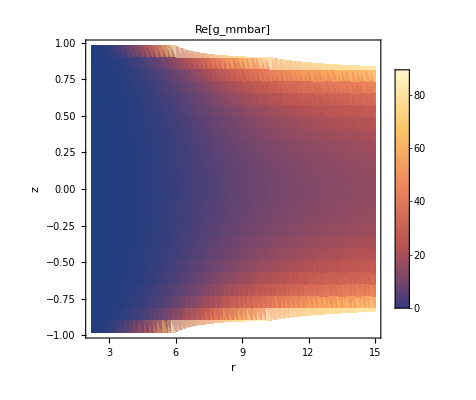

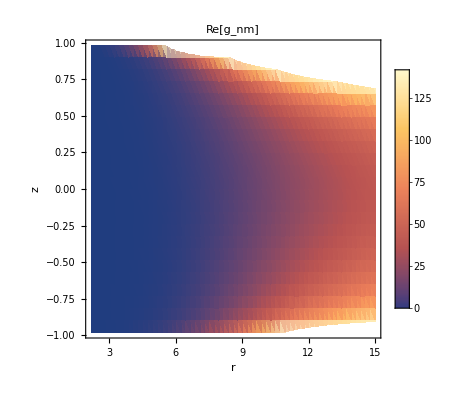

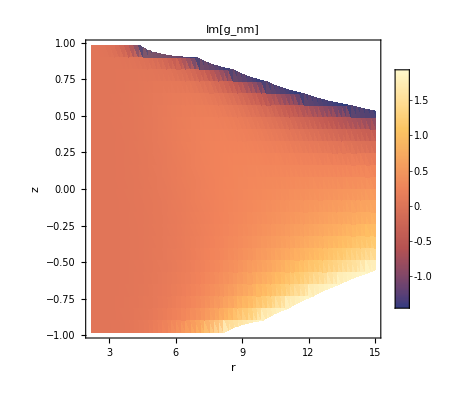

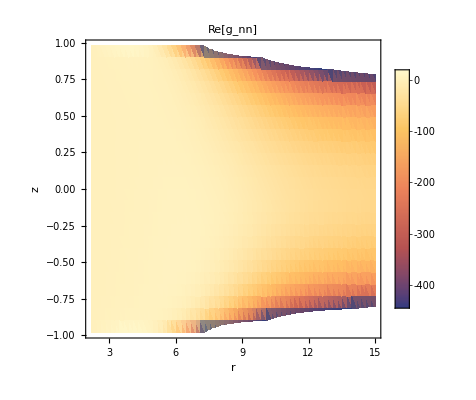

```mathematica
FieldDensityPlot[smoke["FieldXmmb"],Re,"Re[g_mmbar]"]
FieldDensityPlot[smoke["FieldXnm"],Re,"Re[g_nm]"]
FieldDensityPlot[smoke["FieldXnm"],Im,"Im[g_nm]"]
FieldDensityPlot[smoke["FieldXnn"],Re,"Re[g_nn]"]
```